```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"};
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"};

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["ImageModeling.m"]
```

## Preliminaries

```mathematica
SetOptions[ArrayPlot,PlotLegends->Automatic,ColorFunction->ColorData["CherryTones"]];
```

There is some freedom in defining the form of the fast Fourier transform. Here I choose the convention that is used in the Art of Scientific Computing (latest edition).

```mathematica
fourierParametersMATLAB={1,-1};
fourierParametersAoC={1,1};
SetOptions[Fourier,FourierParameters->fourierParametersAoC];
SetOptions[InverseFourier,FourierParameters->fourierParametersAoC];
```

## 1D test

```mathematica
dim=2^7
gauss1d[x_,sigma_,mu_]:=(1/(Sqrt[2*Pi]*sigma))*Exp[-0.5((x-mu)/sigma)^2];
lambda=1.;
min=-20*lambda;
max=20*lambda;
delta=(max-min)/(dim-1);
```

128

```mathematica
arrayGauss1d=Table[gauss1d[x,1,0],{x,min,max,delta}];
```

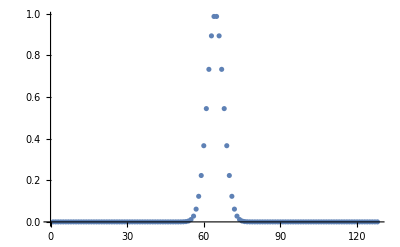

```mathematica
ListPlot[arrayGauss1d*Sqrt[2*Pi],PlotRange->All]
```

Note that the ordering of the output of Fourier appears to be the zero frequency term first, then increasing positive frequency terms, followed by the most negative frequency term, working back on up to the smallest negative frequency term, e.g. 0, 1, 2, 3, ±4,-3, -2, -1.

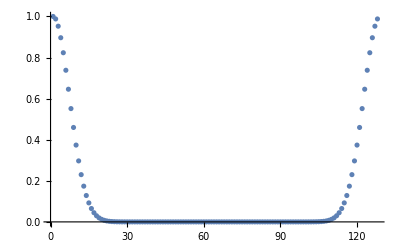

```mathematica
arrayGauss1dFT=delta*Fourier[arrayGauss1d];
ListPlot[Abs@arrayGauss1dFT,PlotRange->All]
```

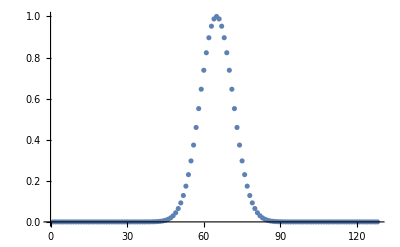

```mathematica
ListPlot[Abs@(#[[dim/2+1;;]]~Join~#[[1;;dim/2]])&[arrayGauss1dFT],PlotRange->All]
```

## 2d test

```mathematica
dim=2^8
lambda=1.;
min=-500*lambda;
max=500*lambda;
delta=(max-min)/(dim-1);
objectWidth=50*lambda;
Print["Spatial pixel size [lambda] = "<>ToString[delta]];
Print["Array size: "<>ToString[dim^2]];
```

256

Spatial pixel size [lambda] = 3.92157

Array size: 65536

```mathematica
(targetArrayGauss=Parallelize@Table[Exp[-(x^2+y^2)/(objectWidth^2)],{x,min,max,delta},{y,min,max,delta}];)//Timing
```

{0.140625,Null}

```mathematica
ArrayPlot[targetArrayGauss]
```

-Graphics-

```mathematica
(targetArrayDot=Parallelize@Table[Boole[(x^2+y^2)≤objectWidth^2],{x,min,max,delta},{y,min,max,delta}]);
ArrayPlot[%]
Dimensions@targetArrayDot
```

-Graphics-

{256,256}

## Fourier transforms

```mathematica
ArrayPlot@Abs@(delta^2*Fourier[targetArrayDot])
```

-Graphics-

```mathematica
ArrayPlot[Abs@Transpose[RotateLeft[Transpose[RotateLeft[delta^2*Fourier[targetArrayDot,FourierParameters->fourierParametersAoC],dim/2]],dim/2]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
ArrayPlot[Abs@rearrange2DFourierArray[delta^2*Fourier@targetArrayGauss]]
```

-Graphics-

```mathematica
ArrayPlot@Abs@InverseFourier@Fourier@targetArrayGauss
```

-Graphics-

## transfer function

Note that this may have to propagate the field over a millimeter to fully encompass the cloud, which is thousands of wavelengths.

```mathematica
deltaf=1/(dim*delta);
k0p=2*Pi/lambda;
fNyquist=1/(2*delta)
fmin=-fNyquist;
fmax=fNyquist-deltaf;
```

0.1275

```mathematica
transferArray[delz_]:=Table[opticalTransferFunction[delz,k0p,{2*Pi*fx,2*Pi*fy}],{fx,fmin,fmax,deltaf},{fy,fmin,fmax,deltaf}];
```

```mathematica
ArrayPlot[Arg@transferArray[2500/Pi],ColorFunction->ColorData["TemperatureMap"]]
```

-Graphics-

```mathematica
psfPutra[delz_,k0_,rPerp_]:=Module[
{x=rPerp[[1]],
y=rPerp[[2]]},
Return[(k0/delz)*Exp[I*Pi*(-1/2+k0*rPerp.rPerp/delz)]];
];
psfGoodman[delz_,k0_,rPerp_]:=Module[
{},
Return[k0*Exp[I*k0(delz+rPerp.rPerp/(2*delz))]/(I*2*Pi*delz)];
];
psfArray[delz_]:=Table[psfGoodman[delz,k0p,{x,y}],{x,min,max,delta},{y,min,max,delta}]
```

```mathematica
Dimensions@psfArray[50]
```

{256,256}

-Graphics-

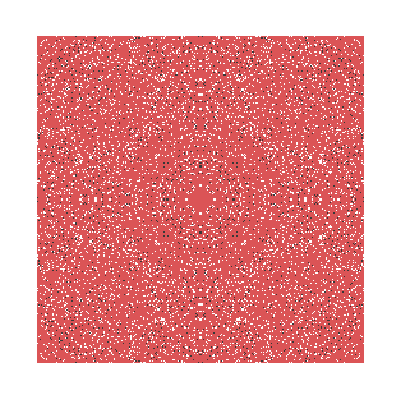

```mathematica
ArrayPlot[Arg@psfArray[1000],ColorFunction->ColorData["TemperatureMap"]]
ArrayPlot@Abs@psfArray[1000]
```

```mathematica
Dimensions@transferArray[1]
```

{256,256}

```mathematica
propField[delz_,target_]:=(*deltaf^2**)(*rearrange2DFourierArray@*)InverseFourier[transferArray[delz]*rearrange2DFourierArray@Fourier@target];
```

```mathematica
deltazp=2500/Pi;
ArrayPlot[Abs@propField[deltazp,targetArrayGauss],ColorFunctionScaling->False]
Max@Abs@propField[deltazp,targetArrayGauss]
```

-Graphics-

0.991881

```mathematica
propFieldGoodman[delz_,target_]:=(*rearrange2DFourierArray@*)ListConvolve[psfArray[delz],target,1];
deltazp=6000/Pi;
ArrayPlot[Abs@propFieldGoodman[deltazp,targetArrayGauss],ColorFunctionScaling->False]
```

-Graphics-

```mathematica
propFieldGoodman[deltazp,targetArrayGauss]
```

{{0.0272296-0.0562055 ⅈ,0.0269931-0.0551207 ⅈ,0.0265979-0.0533565 ⅈ,250,0.0269931-0.0551207 ⅈ,0.0272296-0.0562055 ⅈ,0.0273084-0.0565715 ⅈ},254,{1}}
 |  |  |  |

```mathematica
ListConvolve[psfArray[deltazp],targetArrayGauss,1]
```

{{0.0272296-0.0562055 ⅈ,0.0269931-0.0551207 ⅈ,0.0265979-0.0533565 ⅈ,250,0.0269931-0.0551207 ⅈ,0.0272296-0.0562055 ⅈ,0.0273084-0.0565715 ⅈ},254,{1}}
 |  |  |  |

## absorption function

```mathematica
zdim=dim;
sigma0=6*Pi/k0p^2
```

0.477465

```mathematica
cloudWidth=10*lambda;
z0Cloud=0;
maxOD=1;
rho[x_,y_,z_]:=((maxOD/sigma0)/(Sqrt[2*Pi]*cloudWidth))*Exp[-0.5*((z-z0Cloud)/cloudWidth)^2]*Exp[-0.5*(y/cloudWidth)^2]*Exp[-0.5*(x/cloudWidth)^2];
rho[0,0,0]
```

0.0835543

```mathematica
(*chi[x_,y_,z_,fieldIntensity_,delta_,linewidth_,saturationIntensity_]:=Module[
{rInt=fieldIntensity/saturationIntensity,
rDet=2*delta/linewidth},
Return[(sigma0/k0p)*(I-rDet)*rho[x,y,z]/(1+rInt+rDet^2)];
];*)
```

```mathematica
chiArray=Parallelize@Table[(I*sigma0/k0p)*rho[x,y,z],{x,min,max,delta},{y,min,max,delta},{z,min,max,delta}];
```

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1043.62] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-855.844] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1230.47] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1230.47] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1250.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1230.47] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-746.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-905.21] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1079.76] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
chiArray[[dim/2,dim/2,dim/2]]
```

0.+0.00599355 ⅈ

```mathematica
uniformArray=Table[1,{x,min,max,delta},{y,min,max,delta}];
```

Note that the integral is replaced by delta*Total[].

```mathematica
absorption[z0Pix_,z1Pix_]:=Exp[I*(k0p/2)*delta*Total[chiArray[[All,All,z0Pix;;z1Pix]],{3}]];
```

```mathematica
Dimensions@chiArray
```

{256,256,256}

```mathematica
Max[-Log[Abs[absorption[1,255]*uniformArray]^2]]
```

0.962283

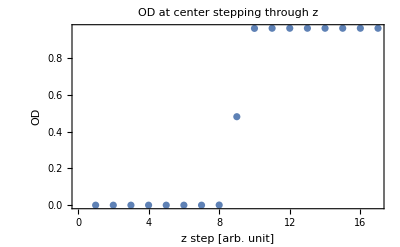

```mathematica
ListPlot[(-Log[Abs[absorption[1,#][[dim/2,dim/2]]]^2])&/@Range[dim/4,3*dim/4,dim/32],PlotLabel->"OD at center stepping through z",Frame->True,FrameLabel->{"z step [arb. unit]","OD"}]
```

```mathematica
ArrayPlot[-Log[Abs[absorption[1,3*dim/4]*uniformArray]^2],ColorFunctionScaling->True,ColorFunction->ColorData["DarkRainbow"]]
```

-Graphics-

```mathematica
aArray=Table[a[x,y,z],{x,3},{y,3},{z,3}]
```

{{{a[1,1,1],a[1,1,2],a[1,1,3]},{a[1,2,1],a[1,2,2],a[1,2,3]},{a[1,3,1],a[1,3,2],a[1,3,3]}},{{a[2,1,1],a[2,1,2],a[2,1,3]},{a[2,2,1],a[2,2,2],a[2,2,3]},{a[2,3,1],a[2,3,2],a[2,3,3]}},{{a[3,1,1],a[3,1,2],a[3,1,3]},{a[3,2,1],a[3,2,2],a[3,2,3]},{a[3,3,1],a[3,3,2],a[3,3,3]}}}

```mathematica
aArray[[All,All,1;;2]]
```

{{{a[1,1,1],a[1,1,2]},{a[1,2,1],a[1,2,2]},{a[1,3,1],a[1,3,2]}},{{a[2,1,1],a[2,1,2]},{a[2,2,1],a[2,2,2]},{a[2,3,1],a[2,3,2]}},{{a[3,1,1],a[3,1,2]},{a[3,2,1],a[3,2,2]},{a[3,3,1],a[3,3,2]}}}

```mathematica
Total[aArray,{3}]//TableForm
```

a[1,1,1]+a[1,1,2]+a[1,1,3] | a[1,2,1]+a[1,2,2]+a[1,2,3] | a[1,3,1]+a[1,3,2]+a[1,3,3]
a[2,1,1]+a[2,1,2]+a[2,1,3] | a[2,2,1]+a[2,2,2]+a[2,2,3] | a[2,3,1]+a[2,3,2]+a[2,3,3]
a[3,1,1]+a[3,1,2]+a[3,1,3] | a[3,2,1]+a[3,2,2]+a[3,2,3] | a[3,3,1]+a[3,3,2]+a[3,3,3]